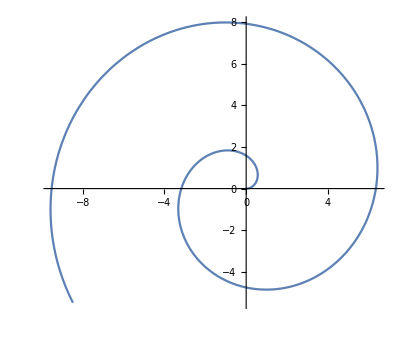

```mathematica
PolarPlot[E^0.01t,{t,0,10} ]
```

```mathematica
(*transforms all values into (-Pi, Pi] interval *)
Clear[x,g];
g[x_/;x>0&&Mod[x,2Pi]≠0]:=x-Floor[x/2/Pi]*2Pi - Pi;
g[x_/;x<0&&Mod[x,2Pi]≠0]:=x+Ceiling[Abs@x/2/Pi]*2pi - Pi;
g[x_/;x==0]:=Pi;
g[x_]:=Pi
```

```mathematica
CoordinateTransform["Polar"->"Cartesian",{0.1,Pi}]
```

{-0.1,0.}

```mathematica
sp=Line@CoordinateTransform["Polar"->"Cartesian",Table[{t, g[t]},{t,0.1,100,1.5}]];
```

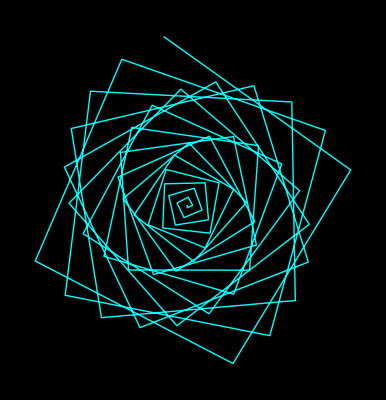

```mathematica
Graphics[{Cyan,Thick,sp},Background->Black]
```

```mathematica
Export["spiral.png", %, ImageResolution->1000]
```

spiral.png